## Prepare

Some parameters to be used

```mathematica
SetDirectory@NotebookDirectory[]
imgSize=Large
```

/Users/leima/GitHub/WhyMathematica/Physics/andersonLocalization

Large

## Anderson Localization Demonstration

This notebook demonstrates the Anderson Localization using MatrixPlot or ArrayPlot.

### Define Parameters

Define the dimonsion of the matrix

```mathematica
dim = 200;
```

### Construct Matrices

Construct two matrices, one with random tridiagonal elements the other with 0.1 for second diagonal elements.

```mathematica
matRandom=SparseArray[{Band[{2,1}]->RandomReal[0.1,dim-1],Band[{1,1}]->1.,Band[{1,2}]->RandomReal[0.1,dim-1]},dim];
```

```mathematica
matRegular=SparseArray[{Band[{2,1}]->0.1,Band[{1,1}]->1.,Band[{1,2}]->0.1},dim];
```

Show the matrix form of these matrices

```mathematica
matRandom//MatrixForm;
```

```mathematica
matRegular//MatrixForm;
```

Plot the matrix themselves

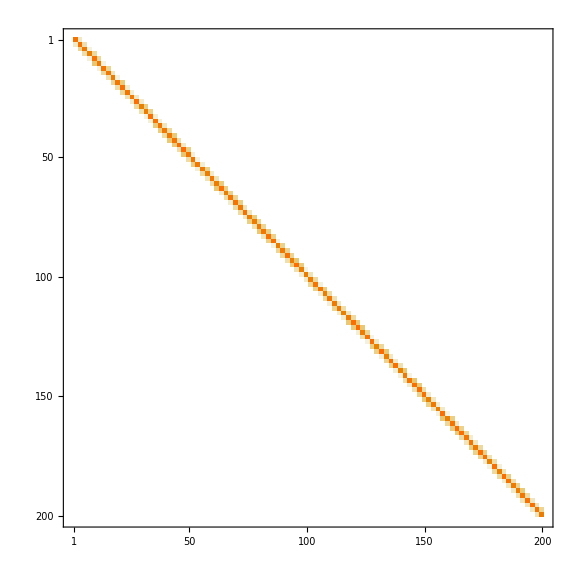

```mathematica
MatrixPlot[matRandom,ImageSize->imgSize]
```

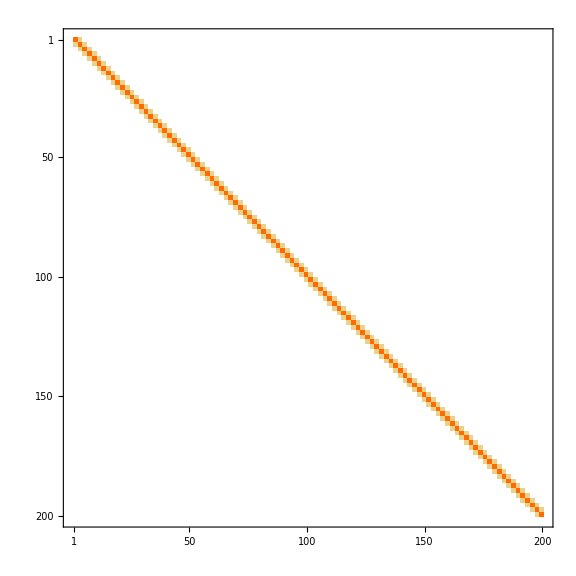

```mathematica
MatrixPlot[matRegular,ImageSize->imgSize]
```

### Find Eigen Vectors

Find the eigen vectors of the matrices

```mathematica
eigVRand=Transpose@Eigenvectors[matRandom]//Quiet;
%//MatrixForm;
```

```mathematica
eigVReg=Transpose@Eigenvectors[matRegular]//Quiet;
%//MatrixForm;
```

### Plot Eigen Vectors

Define frame labes

```mathematica
frameLabel={"# of Elements in Eigen Vectors","# of Eigen Vectors"};
```

Plot the eigen vectors

```mathematica
pltRand=ArrayPlot[eigVRand,PlotLegends->Automatic,ImageSize->imgSize,FrameLabel->frameLabel,FrameTicks->Automatic]
```

-Graphics-

```mathematica
pltReg=ArrayPlot[eigVReg,PlotLegends->Automatic,FrameTicks->Automatic,FrameLabel->frameLabel,ImageSize->imgSize]
```

-Graphics-

### Export Images

```mathematica
Export["pltRand.png",pltRand]
```

pltRand.png

```mathematica
Export["pltReg.png",pltReg]
```

pltReg.png

## Acknowledgement

Thanks to Professor Cahill at University of New Mexico for explaining the idea of Anderson localization to me.
http://theory.phys.unm.edu/cahill/